## Resolución del sistema

```mathematica
Clear[β, Ω, alphaMas, alphaMenos, alphaZ]
```

Valores de los parámetros

```mathematica
β = 0.1; Ω = 0.3;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + (I Ω)/2(1 + x[t]^2)== 0 ,y'[t] == I/2(Ω x[t] - Cos[β t]),z'[t]Exp[-2 y[t]]+ (I Ω)/2 == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Length[(alphaZ)@ValuesOnGrid]
```

8405

## Probabilidades de Transición

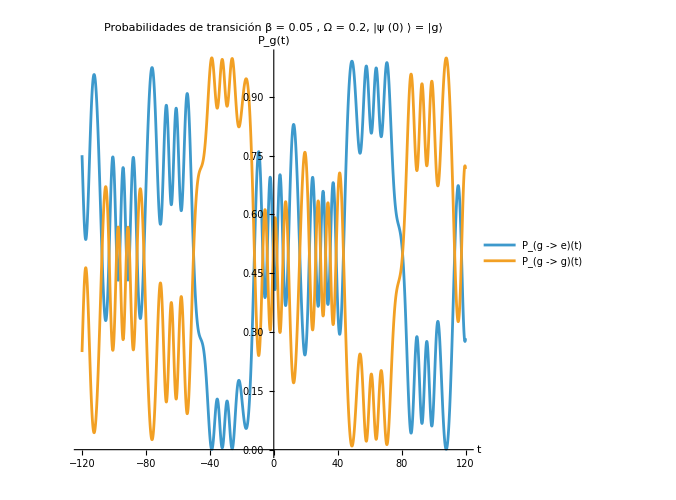

```mathematica
Plot[{(Abs[alphaMas[t]]^2 )Exp[-2Re[alphaZ[t]]], Abs[Exp[- alphaZ[t]] ]^2}, {t, -120, 120}, 
PlotLabel->Style["Probabilidades de transición  β = 0.05 , Ω = 0.2, |ψ (0) ⟩ = |g⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(g -> e)(t)", "P_(g -> g)(t)"},AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_g(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

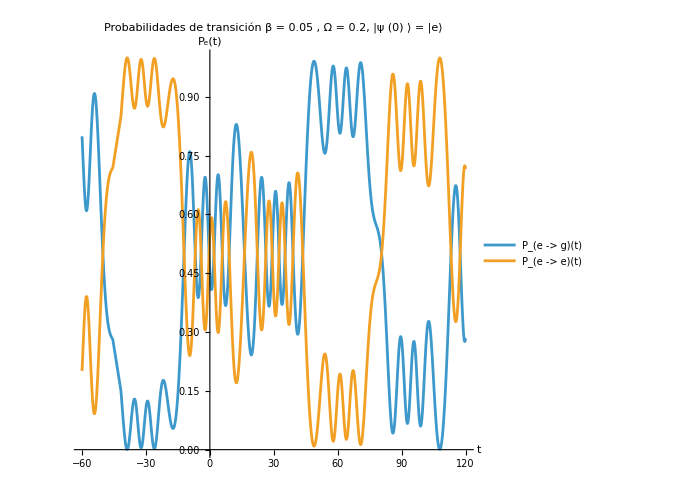

```mathematica
Plot[{(Abs[alphaMenos[t]]^2) Exp[-2Re[alphaZ[t]]], Abs[Exp[alphaZ[t]] + Exp[-alphaZ[t]] alphaMas[t] alphaMenos[t]]^2}, {t, -60, 120}, 
PlotLabel->Style["Probabilidades de transición  β = 0.05 , Ω = 0.2, |ψ (0) ⟩ = |e⟩ ", 16, FontFamily->"Times New Roman", Black],
PlotLegends-> {"P_(e -> g)(t)", "P_(e -> e)(t)"},AxesLabel-> {Style["t",16,FontFamily->"Times New Roman",GrayLevel[0.26]] , Style["P_e(t)",16,FontFamily->"Times New Roman",GrayLevel[0.26]]},
FrameTicksStyle->{{20,2},{20,20}},AspectRatio->1, ImageSize->500]
```

## Espectro EW estado base

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZ[t]]alphaMenos[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S1[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
NumEW3Periodic[Γ_,ν_,Δ_,to_,T_]:=2Γ Exp[-2 Γ T]*(Abs[NIntegrate[Exp[(Γ -I Δ )t+I (1/ν) Sin[ν t]],{t,to,T}]]^2)
```

```mathematica
T0=-200;Γ = 0.1;ν=2.0;
```

```mathematica
ωmin = (ν-2.0)/ν;ωmax = (ν+2.0)/ν;
```

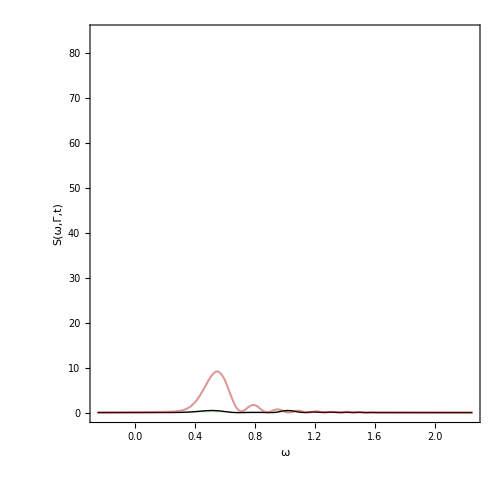

```mathematica
G1 = Show[{ListLinePlot[ParallelTable[{ω,0+S1[0.1,ω*ν -ν,-24,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-24",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,0+NumEW3Periodic[Γ,β,ω*ν-ν,T0,-24]*0.70},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

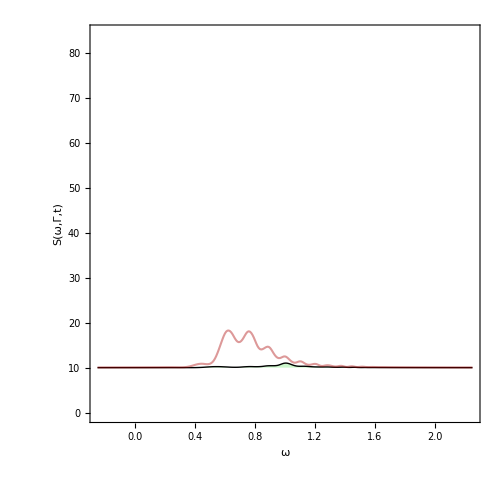

```mathematica
G2 =  Show[{ListLinePlot[ParallelTable[{ω,10+S1[0.1,ω*ν -ν,-16,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-16",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,10+NumEW3Periodic[Γ,β,ω*ν-ν,T0,-16]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

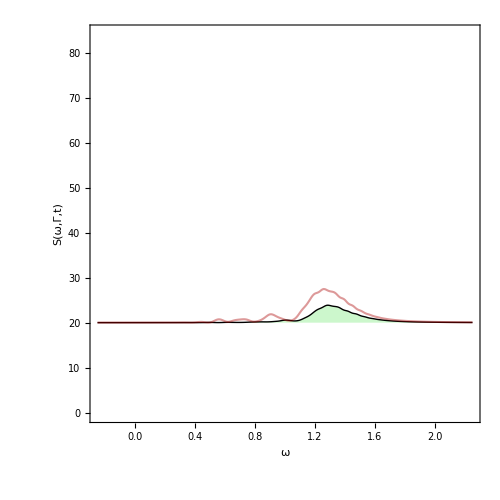

```mathematica
G3 = Show[{ListLinePlot[ParallelTable[{ω,20+S1[0.1,ω*ν -ν,-4,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-4",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,20+NumEW3Periodic[Γ,β,ω*ν-ν,T0,-4]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

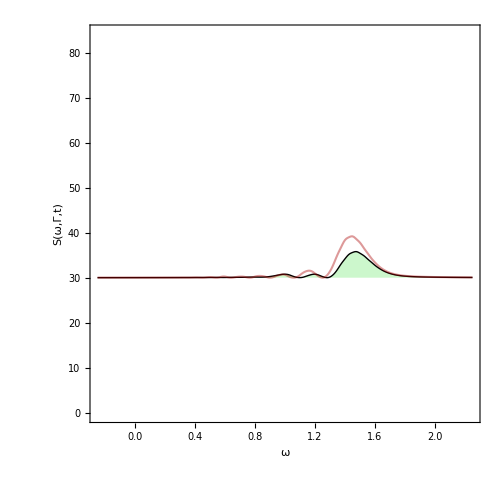

```mathematica
G4 =Show[{ListLinePlot[ParallelTable[{ω,30+S1[0.1,ω*ν -ν,4,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=4",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,30+NumEW3Periodic[Γ,β,ω*ν-ν,T0,4]*0.85},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

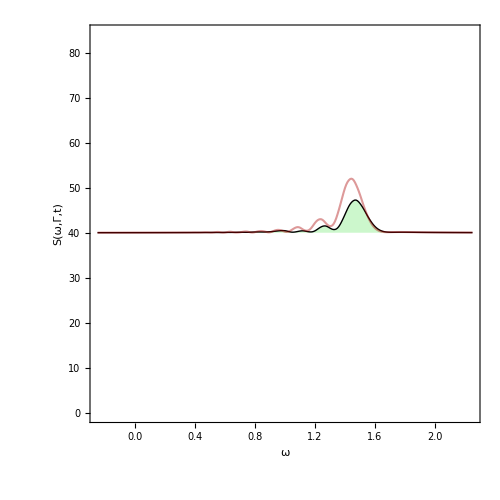

```mathematica
G5 =Show[{ListLinePlot[ParallelTable[{ω,40+S1[0.1,ω*ν -ν,10,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->40,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=10",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,40+NumEW3Periodic[Γ,β,ω*ν-ν,T0,10]*0.85},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

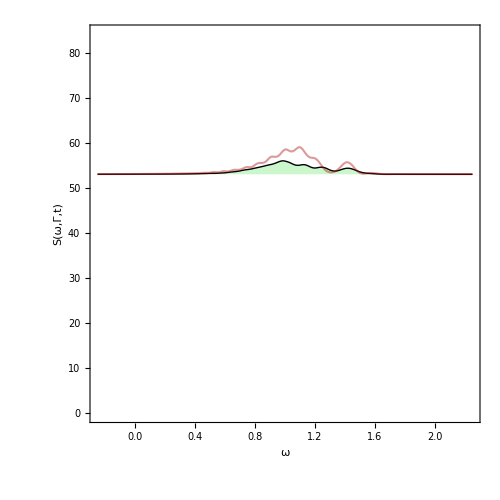

```mathematica
G6 = Show[{ListLinePlot[ParallelTable[{ω,53+S1[0.1,ω*ν -ν,20,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->53,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=20",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,53+NumEW3Periodic[Γ,β,ω*ν-ν,T0,20]*0.85},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

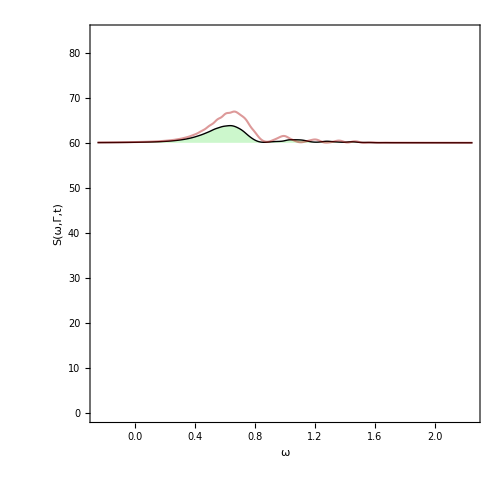

```mathematica
G7 =   Show[{ListLinePlot[ParallelTable[{ω,60+S1[0.1,ω*ν -ν,30,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->60,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=30",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,60+NumEW3Periodic[Γ,β,ω*ν-ν,T0,30]*0.85},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

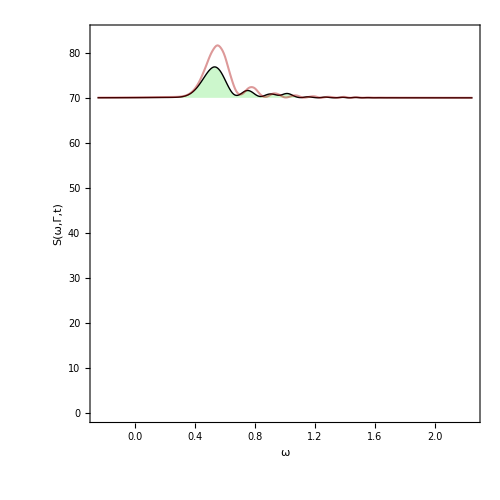

```mathematica
G8 =   Show[{ListLinePlot[ParallelTable[{ω,70+S1[0.1,ω*ν -ν,40,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Filling->70,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]],ListLinePlot[ParallelTable[{ω,70+NumEW3Periodic[Γ,β,ω*ν-ν,T0,40]*0.85},{ω,ωmin,ωmax,(ωmax-ωmin)/300}],PlotRange->{-0.5,84.5},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.003], Opacity[0.4]],
FrameTicksStyle->{{20,2},{16,10}},PlotRangePadding->0,AspectRatio->1, ImageSize->450]}]
```

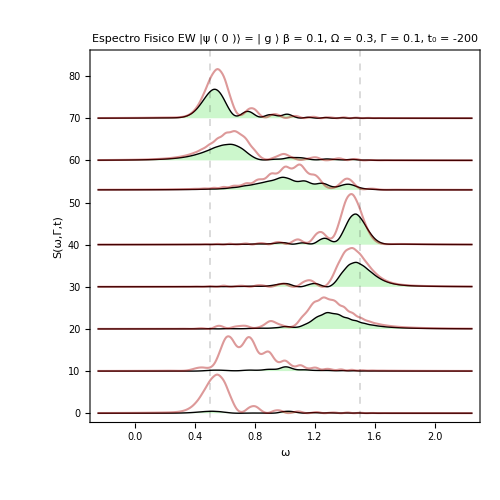

```mathematica
Show[G8,G7,G6,G5,G4,G3,G2,G1,  GridLines->{{{0.5,Directive[Thickness[0.001],Black, Dashed]},{1.5,Directive[Thickness[0.001],Black, Dashed]}},None},PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 )⟩ = | g ⟩ \n β = 0.1, Ω = 0.3, Γ = 0.1, t_0 = -200 ", 18, FontFamily->"Times New Roman", Black]]
```

```mathematica
Export["/home/roberto/Documents/SS_OptCuantica/resultados/limite_cosenoidal",,"PNG"]
```

/home/roberto/Documents/SS_OptCuantica/resultados/limite_cosenoidal

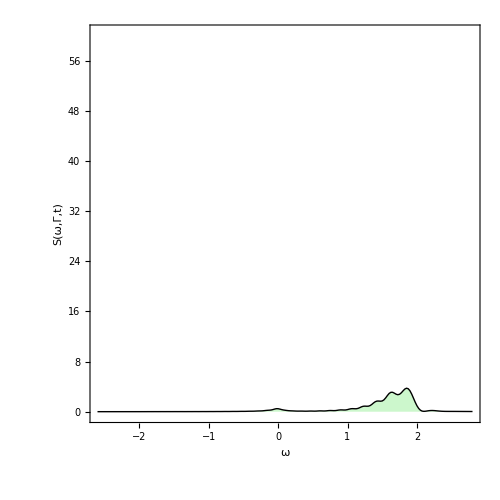

```mathematica
G9 =  ListLinePlot[ParallelTable[{ω,0+S1[0.1,ω,18,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,60.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=18",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

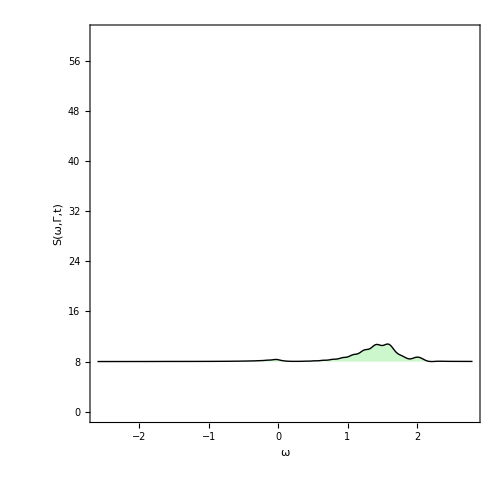

```mathematica
G10 = ListLinePlot[ParallelTable[{ω,8+S1[0.1,ω,22,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,60.5},Filling->8,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=22",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

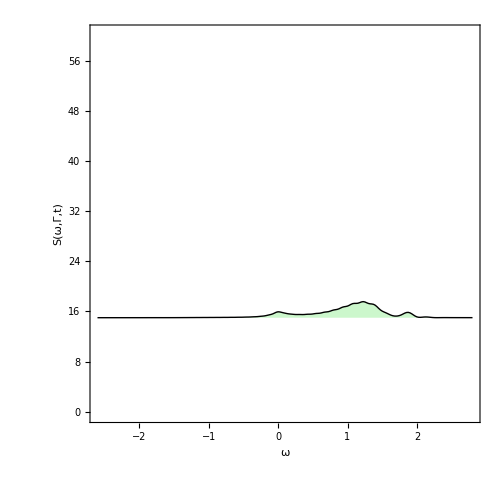

```mathematica
G11 = ListLinePlot[ParallelTable[{ω,15+S1[0.1,ω,25,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,60.5},Filling->15,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=25",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

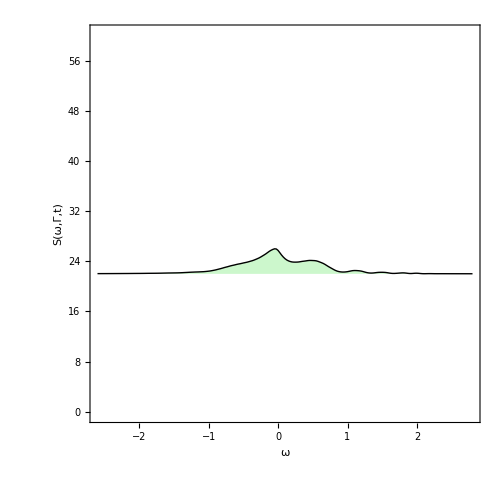

```mathematica
G12 =ListLinePlot[ParallelTable[{ω,22+S1[0.1,ω,35,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,60.5},Filling->22,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=35",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

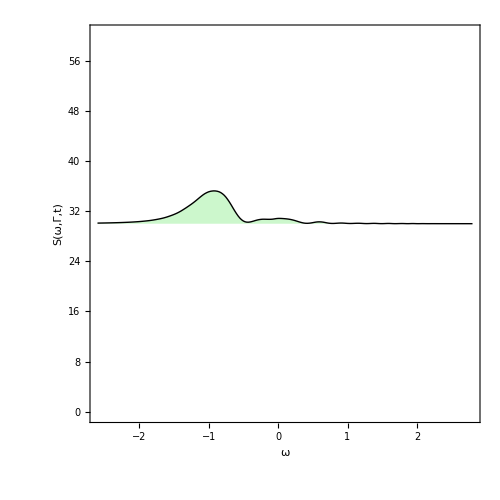

```mathematica
G13 =ListLinePlot[ParallelTable[{ω,30+S1[0.1,ω,46,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,60.5},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=46",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

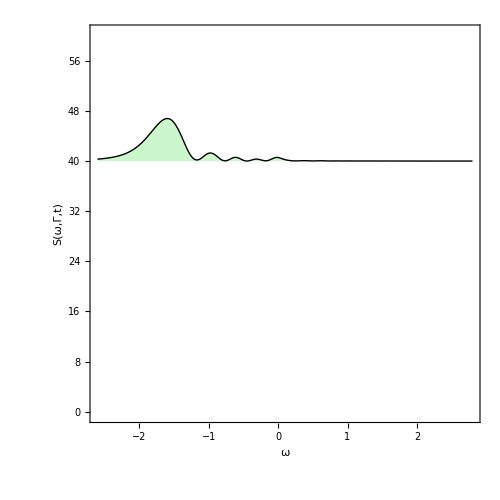

```mathematica
G14 =ListLinePlot[ParallelTable[{ω,40+S1[0.1,ω,56,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,60.5},Filling->40,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=56",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

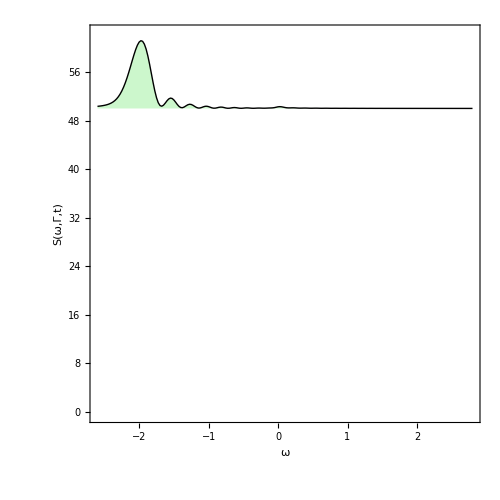

```mathematica
G15 =ListLinePlot[ParallelTable[{ω,50+S1[0.1,ω,70,-200]},{ω,-2.6,2.8,0.025}],PlotRange->{-0.5,62.5},Filling->50,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=70",
FrameLabel->{Style["ω",34,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

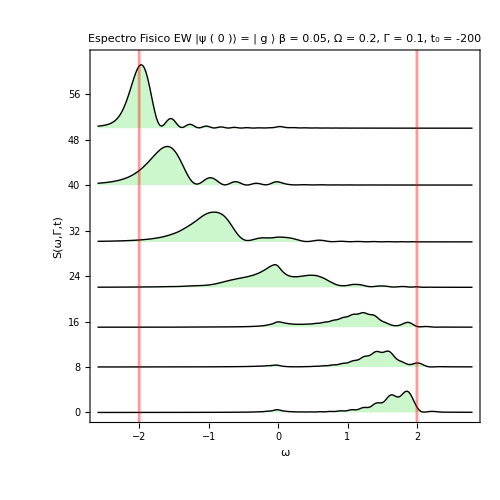

```mathematica
Show[G15,G14,G13,G12,G11,G10,G9, GridLines->{{{-2.0,Directive[Thickness[0.004],Red]},{+2.0,Directive[Thickness[0.004],Red]}},None},PlotLabel->Style["Espectro Fisico EW   |ψ ( 0 )⟩ = | g ⟩ \n β = 0.05, Ω = 0.2, Γ = 0.1, t_0 = -200", 16, FontFamily->"Times New Roman", Black]]
```

## Espectro EW estado excitado

```mathematica
L1[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]]alphaMenos[t], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
L2[Γ_,ω_,T_,T0_]:= Abs[NIntegrate[Exp[(Γ-I ω)t]Exp[-2 alphaZ[t]], {t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S2[Γ_,ω_,T_,T0_]:=2Γ Exp[-2Γ T](L1[Γ,ω,T,T0]+L2[Γ,ω,T,T0])
```

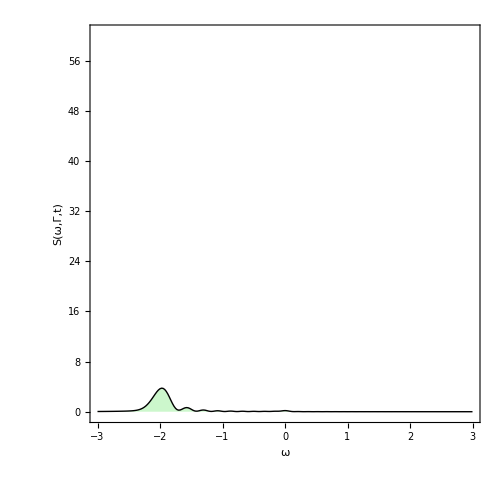

```mathematica
W0 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,-54,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-54",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

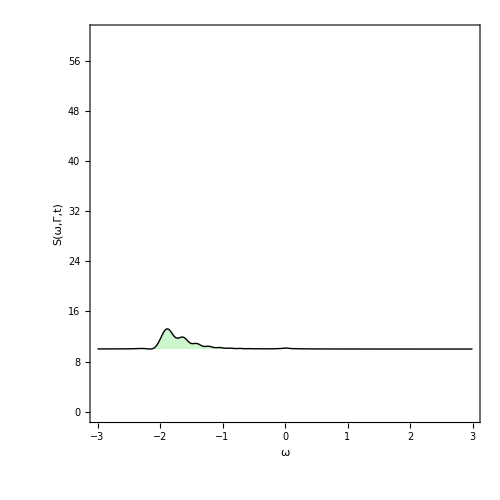

```mathematica
W1 =ListLinePlot[ParallelTable[{ω,10+S2[0.1,ω,-46,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-46",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

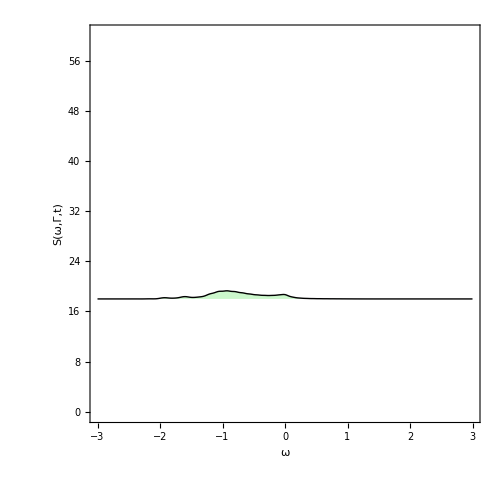

```mathematica
W2 =ListLinePlot[ParallelTable[{ω,18+S2[0.1,ω,-34,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->18,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-34",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

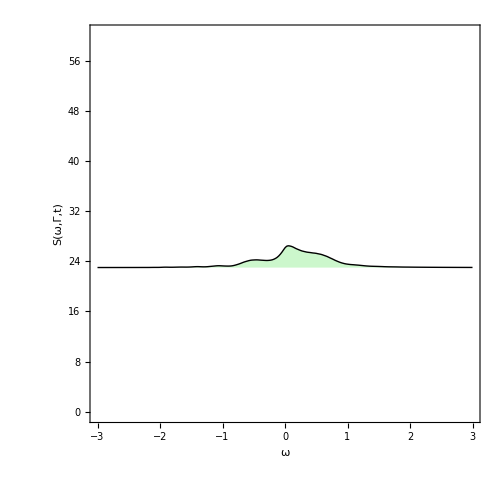

```mathematica
W3 =ListLinePlot[ParallelTable[{ω,23+S2[0.1,ω,-26,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->23,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-26",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

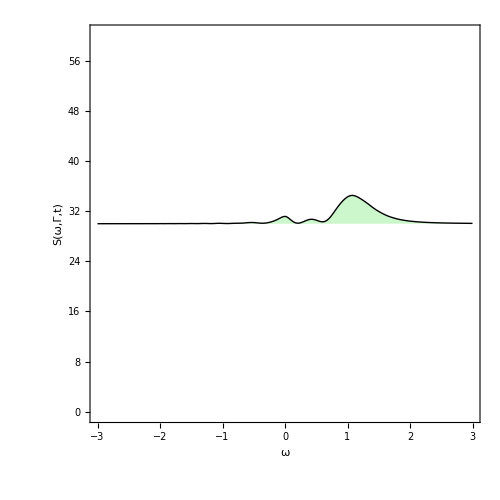

```mathematica
W4 =ListLinePlot[ParallelTable[{ω,30+S2[0.1,ω,-15,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-15",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

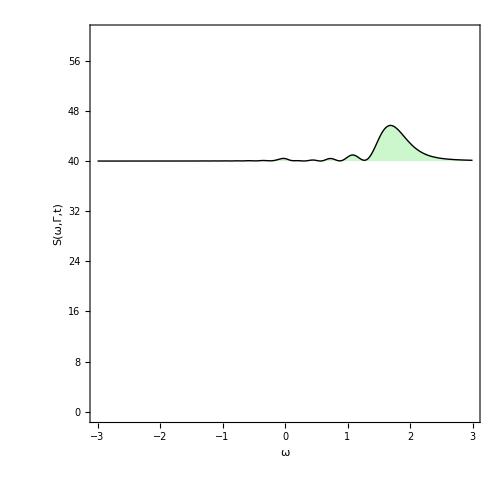

```mathematica
W5 =ListLinePlot[ParallelTable[{ω,40+S2[0.1,ω,-5,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->40,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=-5",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

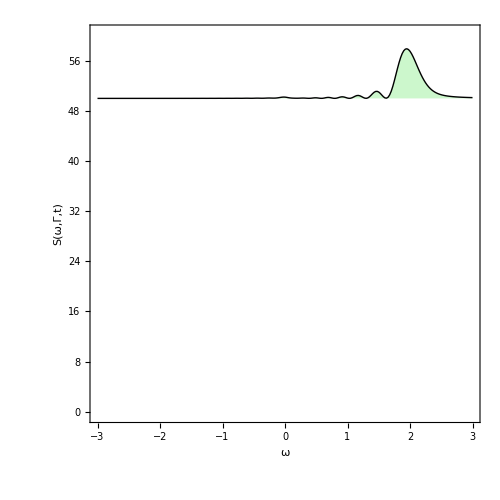

```mathematica
W6 =ListLinePlot[ParallelTable[{ω,50+S2[0.1,ω,4,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->50,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=4",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

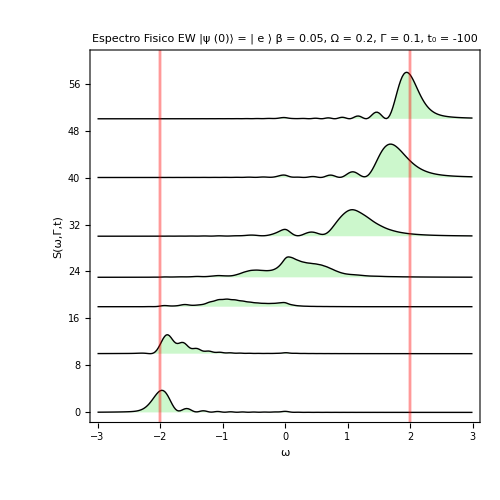

```mathematica
Show[W6,W5,W4,W3,W2,W1,W0,GridLines->{{{-2.0,Directive[Thickness[0.004],Red]},{+2.0,Directive[Thickness[0.004],Red]}},None},PlotLabel->Style["Espectro Fisico EW   |ψ (0)⟩ = | e ⟩ \n β = 0.05, Ω = 0.2, Γ = 0.1, t_0 = -100", 18, FontFamily->"Times New Roman", Black]]
```

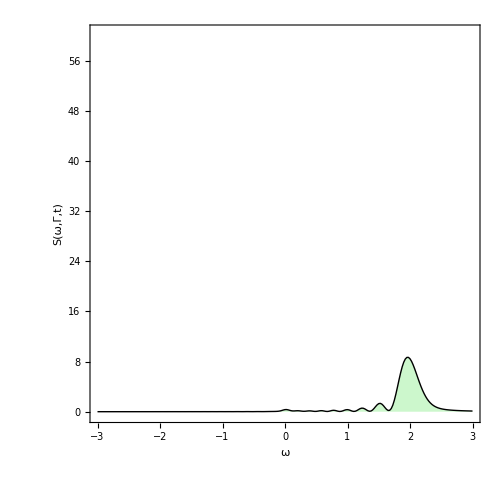

```mathematica
W8 =ListLinePlot[ParallelTable[{ω,0+S2[0.1,ω,6,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->0,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=6",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

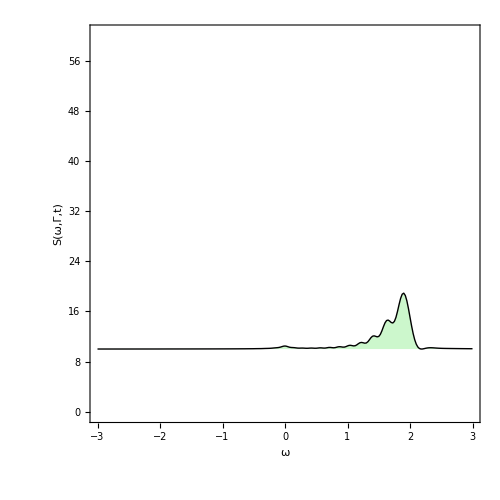

```mathematica
W9 =ListLinePlot[ParallelTable[{ω,10+S2[0.1,ω,16,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->10,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=16",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,
ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

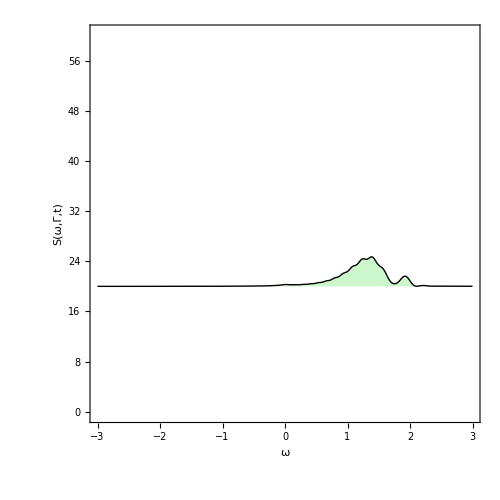

```mathematica
W10 =ListLinePlot[ParallelTable[{ω,20+S2[0.1,ω,24,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->20,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=24",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

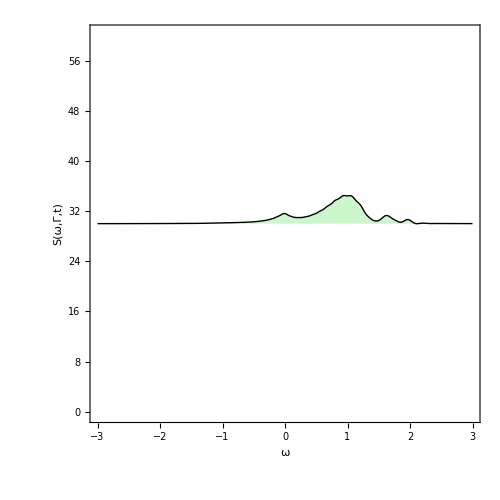

```mathematica
W11 =ListLinePlot[ParallelTable[{ω,30+S2[0.1,ω,28,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->30,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=28",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

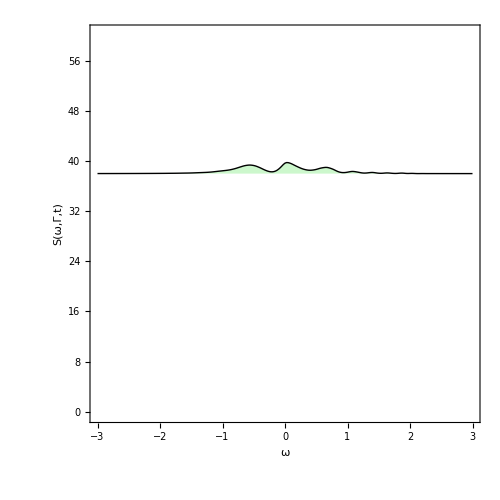

```mathematica
W12 =ListLinePlot[ParallelTable[{ω,38+S2[0.1,ω,40,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->38,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=40",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

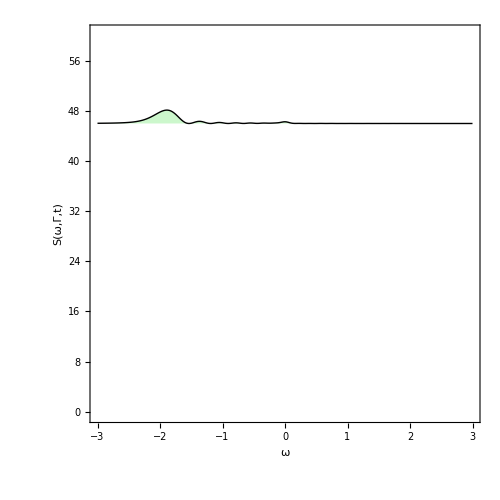

```mathematica
W13 =ListLinePlot[ParallelTable[{ω,46+S2[0.1,ω,64,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->46,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=64",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

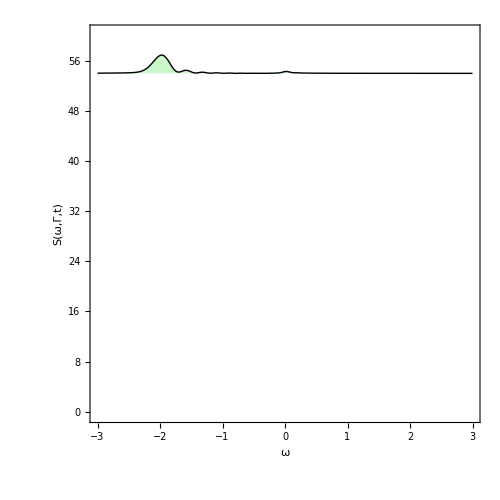

```mathematica
W14 =ListLinePlot[ParallelTable[{ω,54+S2[0.1,ω,72,-200]},{ω,-3,3,0.025}],PlotRange->{-0.5,60.5},Filling->54,Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.002]],PlotLegends->"t=72",
FrameLabel->{Style["ω",24,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",22,FontFamily->"Times New Roman",Gray]},
FrameTicksStyle->{{20,2},{20,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500,FillingStyle->Directive[RGBColor[0.,0.85,0],Opacity[.2]]]
```

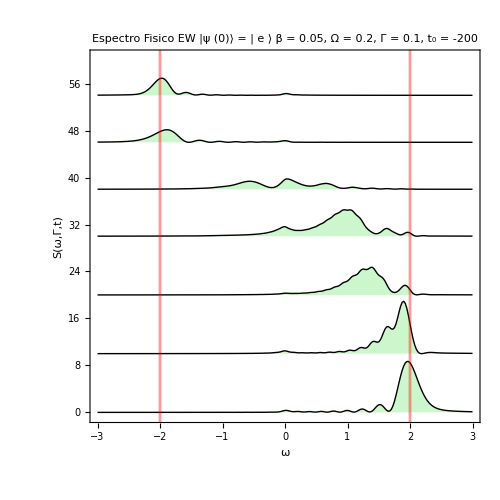

```mathematica
Show[W14,W13,W12,W11,W10,W9,W8,GridLines->{{{-2.0,Directive[Thickness[0.004],Red]},{+2.0,Directive[Thickness[0.004],Red]}},None},
PlotLabel->Style["Espectro Fisico EW   |ψ (0)⟩ = | e ⟩ \n β = 0.05, Ω = 0.2, Γ = 0.1, t_0 = -200", 18, FontFamily->"Times New Roman", Black]]
```